# In silico analysis of corticosteroid-boosted antibiotics treatment for septic arthritis in a hybrid mathematical model

## Antibiotic treatment without corticosteroids

```mathematica
data = Import["C:\\Szakdolgozat\\HAL\\HAL-master\\HAL-master\\CorticosteroidsAntibiotics\\output\\StaphyloExperiments\\AntibioticsOnly\\Out.csv","Data"];
```

Data: tick, healthy, infected, dead, bacteria, immune,  AB, CS

```mathematica
T=5150;
bactData=Table[data[[i]][[5]],{i,1,T}];
immuneData=Table[data[[i]][[6]],{i,1,T}];
ABData=Table[data[[i]][[7]],{i,1,T}];
CSData=Table[data[[i]][[8]],{i,1,T}];
```

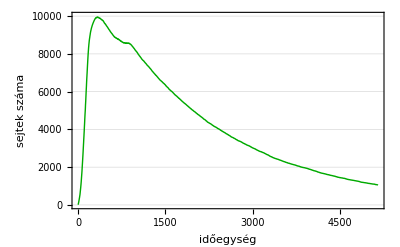

```mathematica
ListLinePlot[
{immuneData},
PlotRange->{0,10000},
LabelStyle->{Black, FontFamily->"Times",20},
PlotStyle->Directive[Thick, Darker[Green]],
GridLines->{None, Automatic},
Frame ->True,
FrameLabel->{"időegység","sejtek száma"}
]
```

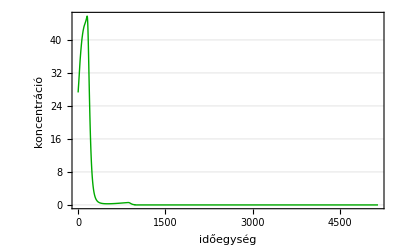

```mathematica
ListLinePlot[
{bactData},
PlotRange->All,
LabelStyle->{Black, FontFamily->"Times",20},
PlotStyle->{Directive[Thick, Darker[Green]],Directive[Thick,Gray]},
GridLines->{None, Automatic},
Frame ->True,
FrameLabel->{"időegység","koncentráció"}]
```

```mathematica
ListLinePlot[
{ABData}, 
PlotRange->All,
LabelStyle->{Black, FontFamily->"Times",20},
PlotLegends->Placed[{"Antibiotikumkoncentráció"},{Center,Below}],
PlotStyle->{Directive[Thick, Darker[Green]]},
GridLines->{None, Automatic},
Frame ->True,
FrameLabel->{"időegység","koncentráció"}]
```

-Graphics-

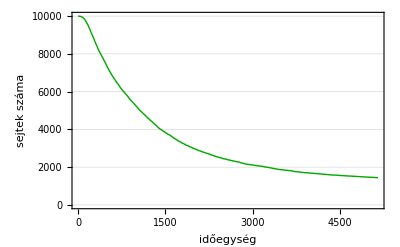

```mathematica
healthyCellData =Table[data[[i]][[2]],{i,1,T}];
ListLinePlot[
{healthyCellData},
PlotRange->{0,10000},
LabelStyle->{Black, FontFamily->"Times",20},
PlotStyle->{Directive[Thick, Darker[Green]]},
GridLines->{None, Automatic},
Frame ->True,
FrameLabel->{"időegység","sejtek száma"}]
```

## Antibiotic treatment with corticosteroids

```mathematica
T=5150
```

5150

```mathematica
dataCStrue = Import["C:\\Szakdolgozat\\HAL\\HAL-master\\HAL-master\\CorticosteroidsAntibiotics\\output\\StaphyloExperiments\\steroidBoostedAB\\Out.csv","Data"];
```

```mathematica
bactData2=Table[dataCStrue[[i]][[5]],{i,1,T}];
immuneData2=Table[dataCStrue[[i]][[6]],{i,1,T}];
ABData2=Table[dataCStrue[[i]][[7]],{i,1,T}];
CSData2=Table[dataCStrue[[i]][[8]],{i,1,T}];
```

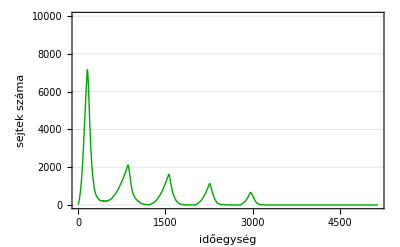

```mathematica
ListLinePlot[
{immuneData2},
PlotRange->{0,10000},
LabelStyle->{Black, FontFamily->"Times",20},
PlotStyle->Directive[Thick, Darker[Green]],
GridLines->{None, Automatic},
Frame ->True,
FrameLabel->{"időegység","sejtek száma"}]
```

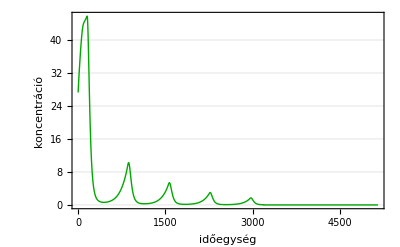

```mathematica
ListLinePlot[
{bactData2}, 
PlotRange->All,
LabelStyle->{Black, FontFamily->"Times",20},
PlotStyle->{Directive[Thick, Darker[Green]],Directive[Thick,Gray],Directive[Thick, Blue]},
GridLines->{None, Automatic},
Frame ->True,
FrameLabel->{"időegység","koncentráció"}]
```

```mathematica
ListLinePlot[
{ABData2,CSData2}, 
PlotRange->All,
LabelStyle->{Black, FontFamily->"Times",20},
PlotLegends->Placed[{"Antibiotikumkoncentráció", "Kortikoszteroidkoncentráció"},{Center, Below}],
PlotStyle->{Directive[Thick, Darker[Green]],Directive[Thick,Pink]},
GridLines->{None, Automatic},
Frame ->True,
FrameLabel->{"időegység","koncentráció"}]/. "Row"->"Column"
```

-Graphics-

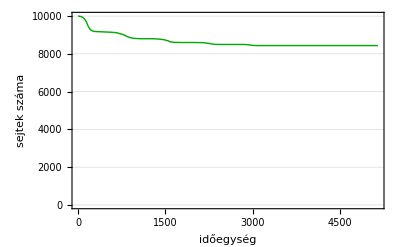

```mathematica
healthyCellData2 =Table[dataCStrue[[i]][[2]],{i,1,T}];
ListLinePlot[
{healthyCellData2},
PlotRange->{0,10000},
LabelStyle->{Black, FontFamily->"Times",20},
PlotStyle->{Directive[Thick, Darker[Green]]},
GridLines->{None, Automatic},
Frame ->True,
FrameLabel->{"időegység","sejtek száma"}]
```